# Trapped-Ions Oxford/Hub virtual device

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz

```mathematica
Options[TrappedIonOxford]={
(*the nodes name together with the total qubits on each node*)
Nodes-><|"Alice"->4,"Bob"->4|>,
T1-><|"Alice"->100, "Bob"->110 |>,
T2-><|"Alice"->40, "Bob"->45|>,
(* duration for moving operations: Split,Combine, and physical swap*)
DurMove-><|"Alice"->4, "Bob"->5|>,

(*fidelity of preparation/initialisation*)
FidInit-><|"Alice"->0.99, "Bob"->0.98|>,
(*fraction of depolarising:dephasing in the initialisation *)
EFInit-><|"Alice"->{1,0}, "Bob"->{1,0}|>,
DurInit-><|"Alice"->2,"Bob"->5|>,

(* Readout: fidelity. It has bitflip error *)
FidRead-><|"Alice"->0.98, "Bob"->0.99|>,
DurRead-><|"Alice"->20, "Bob"->20|>,

(*Fidelity of single x- and y- rotations; z-rotation is instaneous (noiseless, virtual) *)
FidSingleXY-><|"Alice"->0.98, "Bob"->0.99|>,
(*fraction of depolarising:dephasing noise of the x- and y- rotations *)
EFSingleXY-><|"Alice"->{0.2,0.8},"Bob"->{0.1,0.9}|>,
(* rabi frequency on single rotations in MHz *)
RabiFreq-><|"Alice"->5, "Bob"->5 |>,

(* frequency of CZ operation*)
FreqCZ-><|"Alice"->5*10^3,"Bob"->3.3*10^3|>,
(*Fidelity of controlled-Z operation *)
FidCZ-><|"Alice"->0.97, "Bob"->0.96|>,
EFCZ-><|"Alice"->{1,0},"Bob"->{0,1}|>,
(* frequency of remote entanglement *)
FreqEnt->6*10^3,
(* fidelity of remote entanglement *)
FidEnt->0.8,
EFEnt->{1,0}
};
```

Questlink takes initial indices; thus, passive noise is incorrect. Thus, passive noise is manually added for every gate.
Spatial move operations (SplitZ, CombS, PSwap) and quantum operations (the rest) must be done separately to follow the correct zone rules.
CombS, combine string within the zone not yet applied completely? (do one needs to combine string before applying 2-qubit gates?)

native gates:  Init, Read, Rx, Ry, CZ, Ent[node1,node2], SWAP, SplitZ, CombZ  

Zone1 :prepare, store(?), detect
Zone2 :prepare, store, detect, logic
Zone3 :prepare, store, detect, logic
Zone4 :remote entangle

```mathematica
dev=TrappedIonOxford[];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
dev@NumAccessibleQubits
```

8

```mathematica
DestroyAllQuregs[];
ρ=CreateDensityQureg[8];
ψ=CreateQureg[8];
```

```mathematica
InsertCircuitNoise[{Subscript[SplitZ, 2,3]["Alice",3],Subscript[SplitZ, 2,3]["Bob",3]},dev];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
circ1={Subscript[Init, 3]["Alice"],Subscript[Init, 4]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Init, 4]["Bob"]};
DrawCircuit@InsertCircuitNoise[circ1,dev]
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[circ1,dev,ReplaceAliases->True]];
```

-Graphics-

```mathematica
InsertCircuitNoise[{Subscript[SplitZ, 3,4]["Alice",4],Subscript[SplitZ, 3,4]["Bob",4]},dev];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

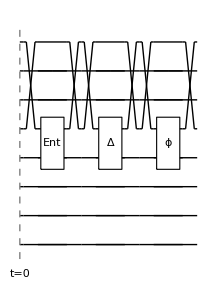

```mathematica
circ2={Subscript[Ent, 4,4]["Alice","Bob"]};
DrawCircuit@InsertCircuitNoise[circ2,dev]
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[circ2,dev,ReplaceAliases->True]];
```

```mathematica
PlotDensityMatrix@ρ
```

-Graphics3D-